# NOTES ON: Basin boundary basics

We create a model problem: In a matrix populated by the numbers 0,1,2, we wish to find the boundaries of islands of 0’s.

```mathematica
a =Table[RandomInteger[4],{20},{20}];
```

```mathematica
boxsize = 13;
dim = First@Dimensions[a];
max = Ceiling[dim/boxsize]
```

2

```mathematica
b=Table[a⟦1+boxsize*(k-1);;Min[boxsize*k,dim],1+boxsize*(j-1);;Min[boxsize*j,dim]⟧//MatrixForm,{k,max},{j,max}]//MatrixForm
```

((3 | 4 | 0 | 2 | 4 | 3 | 4 | 0 | 3 | 3 | 3 | 2 | 3
2 | 2 | 3 | 2 | 2 | 0 | 3 | 0 | 1 | 4 | 4 | 4 | 3
4 | 2 | 2 | 3 | 2 | 1 | 3 | 3 | 4 | 3 | 0 | 2 | 3
4 | 0 | 4 | 2 | 4 | 2 | 4 | 3 | 1 | 2 | 1 | 0 | 2
0 | 3 | 4 | 4 | 4 | 0 | 1 | 1 | 1 | 0 | 2 | 1 | 2
1 | 4 | 4 | 2 | 2 | 3 | 0 | 0 | 4 | 1 | 4 | 3 | 1
1 | 3 | 0 | 2 | 1 | 4 | 4 | 2 | 3 | 1 | 1 | 4 | 3
2 | 1 | 2 | 2 | 2 | 1 | 0 | 2 | 2 | 0 | 4 | 3 | 1
0 | 1 | 1 | 0 | 0 | 4 | 3 | 4 | 3 | 1 | 0 | 2 | 0
4 | 3 | 3 | 2 | 2 | 0 | 3 | 1 | 1 | 2 | 1 | 0 | 0
4 | 1 | 0 | 3 | 0 | 0 | 0 | 1 | 4 | 3 | 0 | 2 | 1
4 | 2 | 2 | 4 | 4 | 3 | 4 | 0 | 1 | 0 | 0 | 2 | 3
0 | 3 | 4 | 4 | 4 | 2 | 4 | 1 | 2 | 0 | 2 | 2 | 0) | (3 | 2 | 3 | 2 | 1 | 0 | 1
1 | 2 | 3 | 4 | 2 | 0 | 2
4 | 4 | 0 | 2 | 4 | 0 | 0
4 | 3 | 1 | 0 | 3 | 3 | 1
4 | 4 | 2 | 4 | 0 | 0 | 2
1 | 4 | 1 | 4 | 3 | 3 | 3
2 | 0 | 0 | 3 | 2 | 4 | 1
0 | 4 | 1 | 1 | 0 | 4 | 0
1 | 2 | 0 | 4 | 2 | 1 | 1
1 | 1 | 0 | 1 | 3 | 1 | 1
1 | 4 | 4 | 0 | 4 | 3 | 0
0 | 1 | 3 | 1 | 1 | 1 | 0
4 | 1 | 1 | 0 | 1 | 3 | 4)
(0 | 2 | 0 | 3 | 4 | 4 | 4 | 4 | 2 | 1 | 3 | 2 | 1
2 | 1 | 4 | 0 | 2 | 4 | 4 | 2 | 0 | 2 | 0 | 0 | 0
0 | 0 | 4 | 3 | 4 | 3 | 0 | 2 | 0 | 4 | 2 | 1 | 4
4 | 2 | 1 | 1 | 3 | 4 | 2 | 4 | 0 | 2 | 2 | 1 | 0
2 | 3 | 3 | 4 | 3 | 2 | 1 | 4 | 1 | 0 | 2 | 1 | 3
4 | 1 | 2 | 4 | 1 | 0 | 3 | 3 | 3 | 1 | 2 | 2 | 2
2 | 1 | 0 | 4 | 0 | 1 | 0 | 1 | 1 | 3 | 4 | 1 | 1) | (4 | 4 | 0 | 4 | 1 | 0 | 2
3 | 2 | 1 | 1 | 2 | 2 | 0
3 | 0 | 0 | 4 | 3 | 1 | 1
4 | 3 | 0 | 2 | 4 | 0 | 3
3 | 4 | 1 | 2 | 0 | 0 | 1
0 | 3 | 4 | 4 | 2 | 4 | 1
3 | 4 | 4 | 0 | 2 | 1 | 3))

```mathematica
a//MatrixForm
```

(3 | 4 | 0 | 2 | 4 | 3 | 4 | 0 | 3 | 3 | 3 | 2 | 3 | 3 | 2 | 3 | 2 | 1 | 0 | 1
2 | 2 | 3 | 2 | 2 | 0 | 3 | 0 | 1 | 4 | 4 | 4 | 3 | 1 | 2 | 3 | 4 | 2 | 0 | 2
4 | 2 | 2 | 3 | 2 | 1 | 3 | 3 | 4 | 3 | 0 | 2 | 3 | 4 | 4 | 0 | 2 | 4 | 0 | 0
4 | 0 | 4 | 2 | 4 | 2 | 4 | 3 | 1 | 2 | 1 | 0 | 2 | 4 | 3 | 1 | 0 | 3 | 3 | 1
0 | 3 | 4 | 4 | 4 | 0 | 1 | 1 | 1 | 0 | 2 | 1 | 2 | 4 | 4 | 2 | 4 | 0 | 0 | 2
1 | 4 | 4 | 2 | 2 | 3 | 0 | 0 | 4 | 1 | 4 | 3 | 1 | 1 | 4 | 1 | 4 | 3 | 3 | 3
1 | 3 | 0 | 2 | 1 | 4 | 4 | 2 | 3 | 1 | 1 | 4 | 3 | 2 | 0 | 0 | 3 | 2 | 4 | 1
2 | 1 | 2 | 2 | 2 | 1 | 0 | 2 | 2 | 0 | 4 | 3 | 1 | 0 | 4 | 1 | 1 | 0 | 4 | 0
0 | 1 | 1 | 0 | 0 | 4 | 3 | 4 | 3 | 1 | 0 | 2 | 0 | 1 | 2 | 0 | 4 | 2 | 1 | 1
4 | 3 | 3 | 2 | 2 | 0 | 3 | 1 | 1 | 2 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 3 | 1 | 1
4 | 1 | 0 | 3 | 0 | 0 | 0 | 1 | 4 | 3 | 0 | 2 | 1 | 1 | 4 | 4 | 0 | 4 | 3 | 0
4 | 2 | 2 | 4 | 4 | 3 | 4 | 0 | 1 | 0 | 0 | 2 | 3 | 0 | 1 | 3 | 1 | 1 | 1 | 0
0 | 3 | 4 | 4 | 4 | 2 | 4 | 1 | 2 | 0 | 2 | 2 | 0 | 4 | 1 | 1 | 0 | 1 | 3 | 4
0 | 2 | 0 | 3 | 4 | 4 | 4 | 4 | 2 | 1 | 3 | 2 | 1 | 4 | 4 | 0 | 4 | 1 | 0 | 2
2 | 1 | 4 | 0 | 2 | 4 | 4 | 2 | 0 | 2 | 0 | 0 | 0 | 3 | 2 | 1 | 1 | 2 | 2 | 0
0 | 0 | 4 | 3 | 4 | 3 | 0 | 2 | 0 | 4 | 2 | 1 | 4 | 3 | 0 | 0 | 4 | 3 | 1 | 1
4 | 2 | 1 | 1 | 3 | 4 | 2 | 4 | 0 | 2 | 2 | 1 | 0 | 4 | 3 | 0 | 2 | 4 | 0 | 3
2 | 3 | 3 | 4 | 3 | 2 | 1 | 4 | 1 | 0 | 2 | 1 | 3 | 3 | 4 | 1 | 2 | 0 | 0 | 1
4 | 1 | 2 | 4 | 1 | 0 | 3 | 3 | 3 | 1 | 2 | 2 | 2 | 0 | 3 | 4 | 4 | 2 | 4 | 1
2 | 1 | 0 | 4 | 0 | 1 | 0 | 1 | 1 | 3 | 4 | 1 | 1 | 3 | 4 | 4 | 0 | 2 | 1 | 3)

One may check the existence of a boundary in a cell via

```mathematica
check[matrix_]:=If[MemberQ[matrix,0,2]&&(MemberQ[matrix,1,2]||MemberQ[matrix,2,2]||MemberQ[matrix,3,2]||MemberQ[matrix,4,2]),1,0]
```

```mathematica
boundaries = Table[check[a⟦1+boxsize*(k-1);;Min[boxsize*k,dim],1+boxsize*(j-1);;Min[boxsize*j,dim]⟧],{k,max},{j,max}]
```

{{1,1},{1,1}}

Refining our box size

```mathematica
boxsize = 2;
dim = First@Dimensions[a];
max = Ceiling[dim/boxsize]
```

10

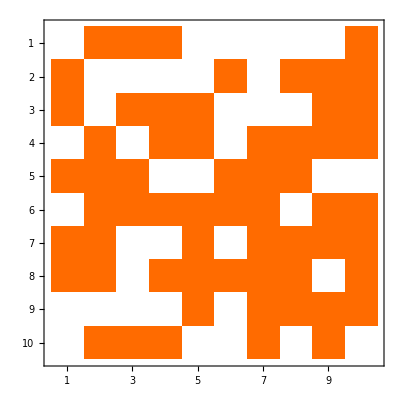

```mathematica
boundaries2 = Table[check[a⟦1+boxsize*(k-1);;Min[boxsize*k,dim],1+boxsize*(j-1);;Min[boxsize*j,dim]⟧],{k,max},{j,max}];
MatrixPlot[boundaries2]
```

This currently checks the existence of a boundary on the lower left corner of each pixel. We may refine our search to check all corners instead.

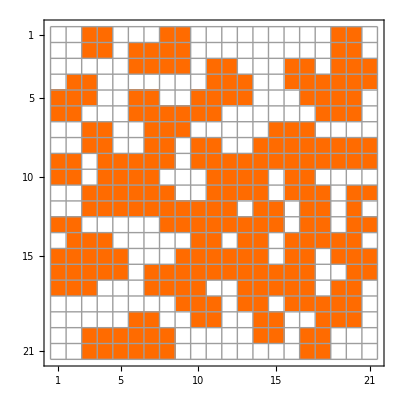

```mathematica
boundaries3 = Table[check[a⟦Max[k,1];;Min[k+boxsize-1,dim],Max[j,1];;Min[j+boxsize-1,dim]⟧],{k,0,dim},{j,0,dim}];
MatrixPlot[boundaries3,Mesh->All]
```

Here each intersection that looks like a ‘+‘ corresponds to a number on the previous matrix. So the first ‘+‘ on the upper left hand corner is the ‘3’ in the original matrix, colored white because it isn’t adjacent to any 0’s. Adjacent on its right represents the number 4, which is beside a 0, so the pixels to the right of the ‘+‘ that represents the 4 is colored orange.